# Derivatives in Multivariate Calculus

## Naman Taggar

```mathematica
save[name_]:=Export[NotebookDirectory[]<>"../../pages/posts/img/"<>name<>".png",%,ImageResolution->200]
```

```mathematica
main=Show[{Plot3D[Sin[x+y],{x,-3,3},{y,-3,3},ColorFunction->(GrayLevel[3-#3]&),ColorFunctionScaling->False,AxesLabel->{"x","y","z"}],Graphics3D[{Opacity[0.3],Blue,InfinitePlane[{1,0,0},{{0,1,0},{0,0,1}}]}],Graphics3D[{Opacity[0.3],Red,InfinitePlane[{0,-1,0},{{1,0,0},{0,0,1}}]}],ParametricPlot3D[{x,-1,Sin[x-1]},{x,1.75,2.75},PlotStyle->Directive[{Red,Thickness[0.0075]}],PlotLabels->Callout["Intersection with y = -1",Above]],ParametricPlot3D[{1,y,Sin[y+1]},{y,0,2},PlotStyle->Directive[{Blue,Thickness[0.0075]}],PlotLabels->Callout["Intersection with x = 1",Above]]},PlotRange->{-1.25,1.25}]
save["pd"]
sub=-Graphics3D-
save["pdsmall"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/pd.png

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/pdsmall.png

```mathematica
f[x_,y_]:=-(x^2+y^2)
{x0, y0}={0,1/4};
{dx,dy}=D[f[x,y],{{x,y}}]/.{x->x0,y->y0};
Show[{
Plot3D[f[x,y],{x,-1,1},{y,-1,1},ColorFunction->(GrayLevel[3-#3]&),ColorFunctionScaling->False,AxesLabel->{"x","y","z"}],
ParametricPlot3D[{x,y0,f[x,y0]},{x,-1,1},PlotStyle->Directive[{Red,Dashed,Thickness[0.005]}],PlotLegends->{"L_x"}],
ParametricPlot3D[{x0,y,f[x0,y]},{y,-1,1},PlotStyle->Directive[{Blue,Dashed,Thickness[0.005]}],PlotLegends->{"L_y"}],
ParametricPlot3D[{x,y0,dx x+f[x0,y0]-x0 dx},{x,-1,1},PlotStyle->Directive[{Red,Thickness[0.005]}],PlotLegends->{"Tangent to L_x"}],
ParametricPlot3D[{x0,y,dy y+f[x0,y0]-y0 dy},{y,-1,1},PlotStyle->Directive[{Blue,Thickness[0.005]}],PlotLegends->{"Tangent to L_y"}],
Graphics3D[{Opacity[0.3],Purple,InfinitePlane[{x0,y0,f[x0,y0]},{{1,0,dx},{0,1,dy}}]}]
},BoxRatios->{1,1,.6},PlotRange->{-1,.25},ViewPoint->{1.5,1,.65}]
save["tangentplane"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/tangentplane.png

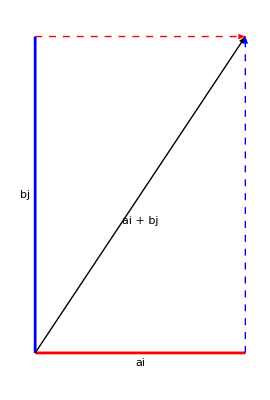

D:\11\website\resources\mm\../../pages/posts/img/dd1.png

```mathematica
Show[
ParametricPlot[{x, 0}, {x, 0,2}, PlotStyle->{Red}],
ParametricPlot[{0, y}, {y, 0,3}, PlotStyle->{Blue}],
Graphics[{
Style[Text["ai", {1, -0.1}], FontSize->14],
Style[Text["bj", {-0.1, 1.5}], FontSize->14],
Style[Rotate[Text["ai + bj", {1, 1.25}], Degree 2/3 90], FontSize->14],
Black,
Arrow[{{0, 0}, {2,3}}],
Red, Dashed,
Arrow[{{0,3}, {2,3}}],
Blue,
Arrow[{{2,0}, {2,3}}]
}],
Axes -> False, PlotRange->All]
save["dd1"]
```

```mathematica
px = 0.5;
py = 1;
vi = 2;
vj = 3;
f[x_, y_]:=Sin[x+y];
dirderiv = Show[{
Plot3D[f[x, y],{x,-.5,1.5},{y,0,1.7},ColorFunction->(GrayLevel[3-#3]&),ColorFunctionScaling->False,AxesLabel->{"x","y","z"}],
ParametricPlot3D[{
px + vi (D[f[x,py], x]/.x->px) t,
py + vj (D[f[px, y], y]/.y->py) t,
f[px + vi (D[f[x,py], x]/.x->px) t,py + vj (D[f[px, y], y]/.y->py) t]
}, {t,-2, 2}, PlotStyle->Directive[{Red, Thickness[0.005]}]],
Graphics3D[{
Red,
PointSize[0.03],Point[{px, py, f[px, py]}],
Opacity[0.3],
InfinitePlane[{px,py,0},{{2,3,0},{2,3,1}}],
Opacity[1], Blue, Thickness[0.005],
Arrow[{{{px, py, f[px, py]+.2}, {px+.4, py+.6, f[px, py]+.2}}}]
}]
}, PlotRange->All]
save["dd2"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/dd2.png